```mathematica
mdwout = "/Volumes/homes/Code/cytomod/shila/semiflexible/out/network/";
mdwlcl="/home/simonfreedman/scratch-midway/cytomod/out/pl/";
mdwhm="/home/simonfreedman/Code/cytomod/shila/semiflexible/out/pl/";
```

```mathematica
ParticleTimeSeries[d_,n_]:=
Module[
{dir=d, name=n},
file=dir<>"/txt_stack/"<>name<>".txt";
particles=Import[file,"Table"];
Print["Finished importing "<>file];
nparticles=Differences[Position[particles,"t",2]][[1,1]]-1;
dt=particles[[2+nparticles,3]];
particlesT=Partition[particles[[2;;]],nparticles, nparticles+1];
{nparticles, dt,particlesT}
];
```

```mathematica
CfgDecorrelationTime[d_]:=
Module[
{dir =d},
{np, dt,rt}=ParticleTimeSeries[d,"rods"];
anglesT=ArcTan[rt[[All,All,3]],rt[[All,All,4]]];
tcorrs=Table[{(j-t)*dt,
Cos[anglesT[[j,i]]-anglesT[[t,i]]]},
{t,1,Length[rt],100},(*Length[rt]},*)
{j,t,Length[rt]},
{i,Length[rt[[t]]]}];
gatheredCorrs = Gather[Flatten[tcorrs,2],First[#1]==First[#2]&];
decor=Table[Mean[gc],{gc,gatheredCorrs}];
decor
];
```

```mathematica
DecorrelationTime[d_]:=
Module[
{dir =d},
{np, dt,rt}=ParticleTimeSeries[d,"rods"];
anglesT=ArcTan[rt[[All,All,3]],rt[[All,All,4]]];
anglesBwT = Table[anglesT[[t,i+1]] -anglesT[[t,i]],
{t,1,Length[anglesT]},
{i,1,Length[anglesT[[t]]]-1}];
tcorrs=Table[{(j-t)*dt,
Cos[(anglesBwT[[j,i]]-anglesBwT[[t,i]])*24]},
{t,1,200},(*Length[anglesBwT],10},*)(*Length[rt]},*)
{j,t,200},(*Length[anglesBwT],10},*)
{i,Length[anglesBwT[[t]]]}];
gatheredCorrs = Gather[Flatten[tcorrs,2],First[#1]==First[#2]&];
decor=Table[Mean[gc],{gc,gatheredCorrs}];
decor
];
```

```mathematica
CCF[d_,decorframe_]:=
Module[
{dir =d,
ndc=decorframe},
{np, dt,rt}=ParticleTimeSeries[d,"rods"];
anglesT=ArcTan[rt[[All,All,3]],rt[[All,All,4]]];
ld=Sqrt[rt[[1,1,3]]^2+rt[[1,1,4]]^2];
corrs=Table[{(j-i)*ld,
Cos[anglesT[[t,j]]-anglesT[[t,i]]]},{t,Ceiling[Length[rt]/2],Length[rt],ndc},
{i,Length[rt[[t]]]},
{j,i,Length[rt[[t]]]}];
gatheredCoors = Gather[Flatten[corrs,2],First[#1]==First[#2]&];
ccf=Table[Mean[gc],{gc,gatheredCoors}];
errs=Table[StandardDeviation[gatheredCoors[[i,All,2]]]/Sqrt[Length[gatheredCoors[[i]]]],{i,Length[gatheredCoors]}];
{ccf,errs}
];
```

```mathematica
seeds=Table[ToString[i],{i,10}];
basedir="nmon50_seed";
dirs=Table[basedir<>s,{s,seeds}];
```

```mathematica
dc=DecorrelationTime[mdwlcl<>dirs[[2]]];
```

Finished importing /home/simonfreedman/scratch-midway/cytomod/out/pl/nmon50_seed2/txt_stack/rods.txt

```mathematica
Length[dc]
```

201

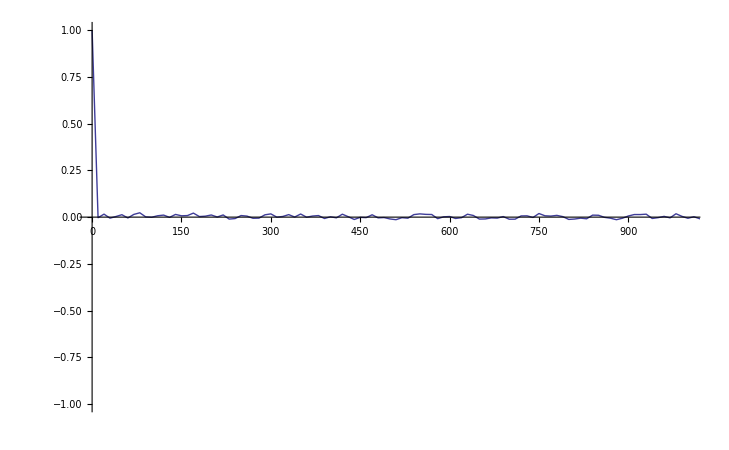

```mathematica
ListLinePlot[dc,PlotRange->{{0,1000},{-1,1}}]
```

```mathematica
Cos[Pi/12.]
```

0.965926

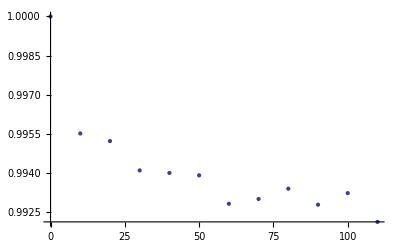

```mathematica
ListPlot[dc]
```

```mathematica
ccfs=Table[CCF[mdwlcl<>dr,400],{dr,{dirs[[2]]}}];
```

Finished importing /home/simonfreedman/scratch-midway/cytomod/out/pl/nmon50_seed2/txt_stack/rods.txt

```mathematica
Length[rt]
```

2001

```mathematica
ccfs[[1,1]]
```

{{0.,1.},{0.8,0.987517},{1.6,0.975871},{2.4,0.960835},{3.2,0.946523},{4.,0.929727},{4.8,0.914959},{5.6,0.89815},{6.4,0.884107},{7.2,0.867633},{8.,0.853164},{8.8,0.839637},{9.6,0.824364},{10.4,0.810322},{11.2,0.786034},{12.,0.757965},{12.8,0.724868},{13.6,0.691382},{14.4,0.656688},{15.2,0.623185},{16.,0.588868},{16.8,0.55482},{17.6,0.522614},{18.4,0.497613},{19.2,0.479076},{20.,0.460094},{20.8,0.444618},{21.6,0.422475},{22.4,0.409013},{23.2,0.390499},{24.,0.370921},{24.8,0.347447},{25.6,0.32629},{26.4,0.294984},{27.2,0.271936},{28.,0.252204},{28.8,0.244887},{29.6,0.257587},{30.4,0.270257},{31.2,0.282661},{32.,0.284278},{32.8,0.295732},{33.6,0.28791},{34.4,0.282804},{35.2,0.279811},{36.,0.279299},{36.8,0.265333},{37.6,0.259378},{38.4,0.256757},{39.2,0.227812}}

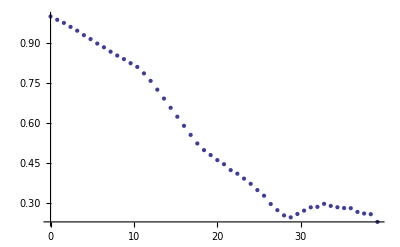

```mathematica
ListPlot[ccfs[[1,1]]]
```

```mathematica
dt
```

10.

```mathematica
ccfs
```

{{{{0.,1.}},{0.}}}

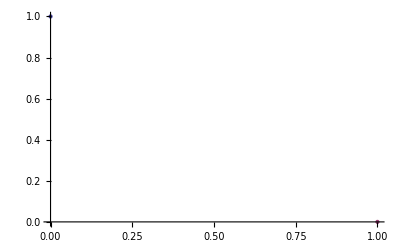

```mathematica
ListPlot[ccfs[[1]]]
```

```mathematica
badccfs={ccfs[[36]]};
```

```mathematica
goodccfs=Delete[ccfs,36];
```

```mathematica
goodccfs=ccfs;
```

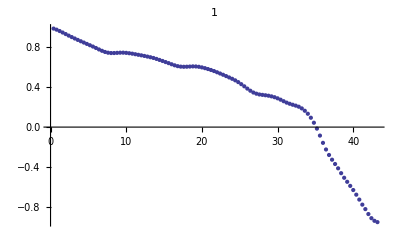
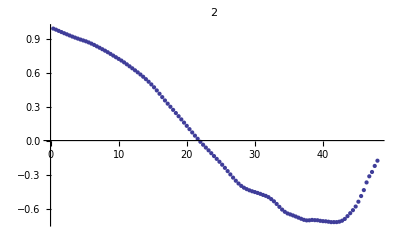
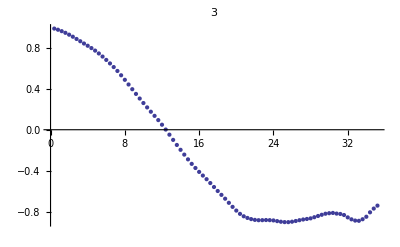
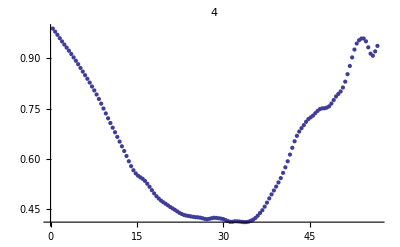
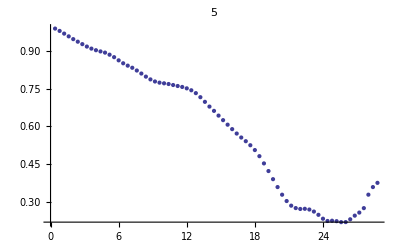
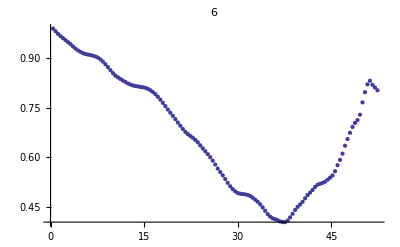
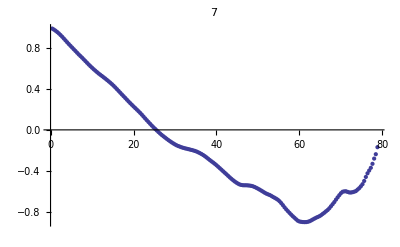
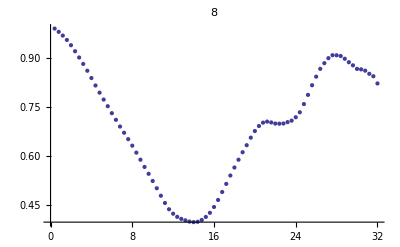

```mathematica
Table[ListPlot[goodccfs[[i,1]],PlotLabel->i],{i,Length[goodccfs]}]
```

```mathematica
nlms=Table[
NonlinearModelFit[
goodccfs[[i,1]],
Exp[-x/(2Lp)],
{Lp},
x,
Weights->1/goodccfs[[i,2]]^2
],
{i,Length[goodccfs]}];
```

NonlinearModelFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

```mathematica
Table[{nlms[[i]]["ParameterTable"],i},{i,Length[nlms]}]//TableForm
```

| Estimate | Standard Error | t-Statistic | P-Value
Lp | 9.76463 | 1.0825 | 9.02046 | 8.3651×10^-15 | 1
 | Estimate | Standard Error | t-Statistic | P-Value
Lp | 7.50975 | 0.877357 | 8.55951 | 4.67789×10^-14 | 2
 | Estimate | Standard Error | t-Statistic | P-Value
Lp | 3.96319 | 0.850439 | 4.66017 | 0.0000112988 | 3
 | Estimate | Standard Error | t-Statistic | P-Value
Lp | 51.9394 | 5.26241 | 9.8699 | 8.60114×10^-18 | 4
 | Estimate | Standard Error | t-Statistic | P-Value
Lp | 16.9815 | 0.535175 | 31.7307 | 1.13037×10^-43 | 5
 | Estimate | Standard Error | t-Statistic | P-Value
Lp | 29.1296 | 0.764792 | 38.0883 | 2.20437×10^-72 | 6
 | Estimate | Standard Error | t-Statistic | P-Value
Lp | 6.98048 | 1.11853 | 6.24075 | 2.6372×10^-9 | 7
 | Estimate | Standard Error | t-Statistic | P-Value
Lp | 36.1511 | 4.74703 | 7.61552 | 4.87151×10^-11 | 8
 | Estimate | Standard Error | t-Statistic | P-Value
Lp | 92.2432 | 8.6827 | 10.6238 | 2.13336×10^-19 | 9
 | Estimate | Standard Error | t-Statistic | P-Value
Lp | 30.8504 | 1.75884 | 17.5403 | 7.65466×10^-33 | 10
 | Estimate | Standard Error | t-Statistic | P-Value
Lp | 184.361 | 22.8758 | 8.05924 | 5.93734×10^-13 | 11
 | Estimate | Standard Error | t-Statistic | P-Value
Lp | 10.1061 | 0.488037 | 20.7077 | 1.37231×10^-43 | 12
 | Estimate | Standard Error | t-Statistic | P-Value
Lp | 9.21583 | 0.359649 | 25.6245 | 1.02835×10^-44 | 13
 | Estimate | Standard Error | t-Statistic | P-Value
Lp | 8.62841 | 0.561432 | 15.3686 | 1.78922×10^-34 | 14
 | Estimate | Standard Error | t-Statistic | P-Value
Lp | 18.9566 | 0.501275 | 37.8168 | 1.24007×10^-77 | 15
 | Estimate | Standard Error | t-Statistic | P-Value
Lp | 121.73 | 23.8861 | 5.09626 | 2.06545×10^-6 | 16
 | Estimate | Standard Error | t-Statistic | P-Value
Lp | 18.6518 | 0.902765 | 20.6608 | 1.17996×10^-41 | 17
 | Estimate | Standard Error | t-Statistic | P-Value
Lp | 10.5975 | 0.650633 | 16.288 | 2.17307×10^-34 | 18
 | Estimate | Standard Error | t-Statistic | P-Value
Lp | 34.8026 | 1.21467 | 28.652 | 4.97138×10^-57 | 19
 | Estimate | Standard Error | t-Statistic | P-Value
Lp | 20.4924 | 0.485626 | 42.1979 | 2.95801×10^-59 | 20
 | Estimate | Standard Error | t-Statistic | P-Value
Lp | 36.2501 | 2.4422 | 14.8432 | 1.98341×10^-24 | 21
 | Estimate | Standard Error | t-Statistic | P-Value
Lp | 111.396 | 11.6342 | 9.57481 | 1.54815×10^-16 | 22
 | Estimate | Standard Error | t-Statistic | P-Value
Lp | 10.3891 | 1.11532 | 9.31485 | 2.12016×10^-16 | 23
 | Estimate | Standard Error | t-Statistic | P-Value
Lp | 8.6712 | 0.791852 | 10.9505 | 5.72349×10^-19 | 24
 | Estimate | Standard Error | t-Statistic | P-Value
Lp | 6.9678 | 0.85714 | 8.12913 | 7.96192×10^-11 | 25
 | Estimate | Standard Error | t-Statistic | P-Value
Lp | 14.0306 | 0.739693 | 18.9682 | 1.2033×10^-39 | 26
 | Estimate | Standard Error | t-Statistic | P-Value
Lp | 5.6344 | 1.57625 | 3.57455 | 0.000459625 | 27
 | Estimate | Standard Error | t-Statistic | P-Value
Lp | 22.4445 | 1.09168 | 20.5596 | 9.15662×10^-36 | 28
 | Estimate | Standard Error | t-Statistic | P-Value
Lp | 14.4698 | 0.244052 | 59.29 | 1.5288×10^-98 | 29
 | Estimate | Standard Error | t-Statistic | P-Value
Lp | 15.5158 | 0.577071 | 26.8871 | 2.01523×10^-61 | 30
 | Estimate | Standard Error | t-Statistic | P-Value
Lp | 45.4673 | 2.12671 | 21.3792 | 4.78144×10^-42 | 31
 | Estimate | Standard Error | t-Statistic | P-Value
Lp | 204.147 | 26.4802 | 7.70942 | 4.57×10^-12 | 32
 | Estimate | Standard Error | t-Statistic | P-Value
Lp | 110.829 | 9.96842 | 11.118 | 5.27775×10^-19 | 33
 | Estimate | Standard Error | t-Statistic | P-Value
Lp | 71.4089 | 4.8522 | 14.7168 | 9.89517×10^-29 | 34
 | Estimate | Standard Error | t-Statistic | P-Value
Lp | 289.271 | 43.7087 | 6.61816 | 1.00299×10^-9 | 35
 | Estimate | Standard Error | t-Statistic | P-Value
Lp | 6.08658 | 1.07931 | 5.6393 | 1.27728×10^-7 | 36
 | Estimate | Standard Error | t-Statistic | P-Value
Lp | 55.5272 | 1.28291 | 43.2822 | 1.07672×10^-76 | 37
 | Estimate | Standard Error | t-Statistic | P-Value
Lp | 165.774 | 23.5427 | 7.04141 | 1.12128×10^-10 | 38
 | Estimate | Standard Error | t-Statistic | P-Value
Lp | 9.88692 | 0.444069 | 22.2644 | 2.49921×10^-40 | 39
 | Estimate | Standard Error | t-Statistic | P-Value
Lp | 34.263 | 1.08245 | 31.6532 | 8.8448×10^-64 | 40
 | Estimate | Standard Error | t-Statistic | P-Value
Lp | 12.6208 | 0.93259 | 13.533 | 1.30741×10^-27 | 41
 | Estimate | Standard Error | t-Statistic | P-Value
Lp | 56.8844 | 2.81746 | 20.1899 | 1.30434×10^-42 | 42
 | Estimate | Standard Error | t-Statistic | P-Value
Lp | 334.6 | 72.4852 | 4.61612 | 8.18714×10^-6 | 43
 | Estimate | Standard Error | t-Statistic | P-Value
Lp | 6.76088 | 0.785059 | 8.61194 | 2.38553×10^-13 | 44
 | Estimate | Standard Error | t-Statistic | P-Value
Lp | 20.2289 | 0.95686 | 21.1409 | 1.25413×10^-39 | 45
 | Estimate | Standard Error | t-Statistic | P-Value
Lp | 321.997 | 58.3447 | 5.51887 | 1.65057×10^-7 | 46
 | Estimate | Standard Error | t-Statistic | P-Value
Lp | 206.513 | 34.6847 | 5.95402 | 4.84319×10^-8 | 47
 | Estimate | Standard Error | t-Statistic | P-Value
Lp | 9.1327 | 0.904094 | 10.1015 | 2.83637×10^-16 | 48
 | Estimate | Standard Error | t-Statistic | P-Value
Lp | 3.94054 | 1.10645 | 3.56143 | 0.000541084 | 49

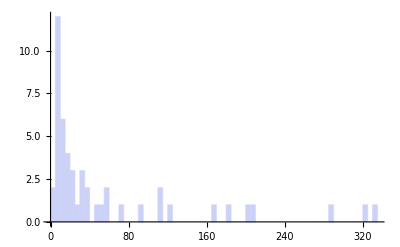

```mathematica
Histogram[Table[nlms[[i]]["ParameterTableEntries"][[1,1]],{i,Length[nlms]}],50]
```

```mathematica
Table[nlms[[i]]["ParameterTableEntries"][[1,1]],{i,Length[nlms]}]
```

{103.952,9.17706,3.48787,16.0874,34.2637,56.4438,62.4622,16.8244,114.852,37.2086,23.6421,8.16769,32.5512,39.9285}